Required cartoons for figure 1(a):

```mathematica
tups=Tuples[{1,2,3,4},2]
```

{{1,1},{1,2},{1,3},{1,4},{2,1},{2,2},{2,3},{2,4},{3,1},{3,2},{3,3},{3,4},{4,1},{4,2},{4,3},{4,4}}

```mathematica
cols=ColorData[97,"ColorList"];
```

```mathematica
base={RGBColor[0.17254901960784313, 0.4823529411764706, 0.7137254901960784],RGBColor[0.8431372549019608, 0.29, 0.29],RGBColor[0.6705882352941176, 0.8509803921568627, 1],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451]};
```

```mathematica
colsnew=base;
```

```mathematica
mat2=tups/.{1->"P",2->"S",3->"D",4->"R"}
```

{{P,P},{P,S},{P,D},{P,R},{S,P},{S,S},{S,D},{S,R},{D,P},{D,S},{D,D},{D,R},{R,P},{R,S},{R,D},{R,R}}

```mathematica
todelete={};
Table[If[i≠j,If[ContainsExactly[tups⟦i⟧,tups⟦j⟧]==True,AppendTo[todelete,{i,j}]]],{i,1,Length[tups]},{j,1,Length[tups]}];
```

```mathematica
del=todelete//Flatten//Union
```

{2,3,4,5,7,8,9,10,12,13,14,15}

```mathematica
Delete[tups,Table[{del[[i]]},{i,Length[del]}]]
```

{{1,1},{2,2},{3,3},{4,4}}

```mathematica
tabmat=Table[{mat2⟦i⟧}//Transpose,{i,Length[mat2]}]
```

{{{P},{P}},{{P},{S}},{{P},{D}},{{P},{R}},{{S},{P}},{{S},{S}},{{S},{D}},{{S},{R}},{{D},{P}},{{D},{S}},{{D},{D}},{{D},{R}},{{R},{P}},{{R},{S}},{{R},{D}},{{R},{R}}}

```mathematica
Table[Export[NotebookDirectory[]<>"comm"<>ToString[i]<>".pdf",ArrayPlot[tabmat⟦i⟧,ColorRules->{"P"->base⟦1⟧,"S"->base⟦2⟧,"D"->base⟦3⟧,"R"->base⟦4⟧},Epilog->{Black,MapIndexed[Style[Text[#1,Reverse[#2-1/2]],Black,80]&,Reverse[tabmat⟦i⟧],{2}]},Mesh->True,MeshStyle->Black]],{i,1,Length[tabmat],1}]
```

{/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm1.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm2.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm3.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm4.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm5.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm6.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm7.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm8.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm9.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm10.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm11.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm12.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm13.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm14.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm15.pdf,/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/comm16.pdf}

Now we make the cartoon for figure 1(b):

```mathematica
mat = {{"P","S","D"},{"S","D","P"},{"D","P","S"}}
```

{{P,S,D},{S,D,P},{D,P,S}}

```mathematica
base={RGBColor[0.17254901960784313, 0.4823529411764706, 0.7137254901960784],RGBColor[0.8431372549019608, 0.29, 0.29],RGBColor[0.6705882352941176, 0.8509803921568627, 1],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451]};
```

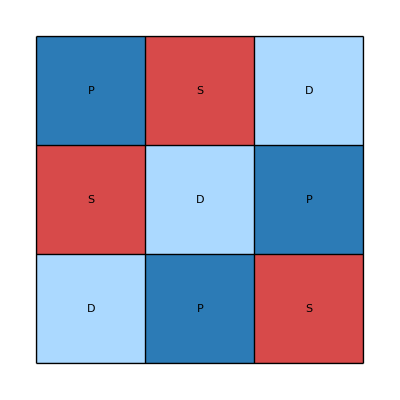

```mathematica
final = ArrayPlot[mat,ColorRules->{"P"->base⟦1⟧,"S"->base⟦2⟧,"D"->base⟦3⟧,"R"->base⟦4⟧},Epilog->{Black,MapIndexed[Style[Text[#1,Reverse[#2-1/2]],Black,50]&,Reverse[mat],{2}]},Mesh->True,MeshStyle->Black]
```

Individual nodes of the interaction graph:

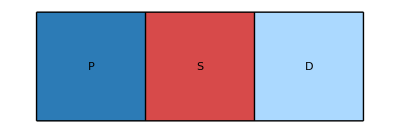

```mathematica
ArrayPlot[{mat[[1]]},ColorRules->{"P"->base⟦1⟧,"S"->base⟦2⟧,"D"->base⟦3⟧,"R"->base⟦4⟧},Epilog->{Black,MapIndexed[Style[Text[#1,Reverse[#2-1/2]],Black,50]&,Reverse[{mat[[1]]}],{2}]},Mesh->True,MeshStyle->Black]
```

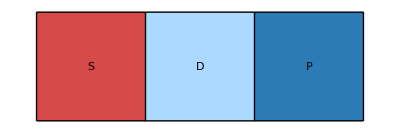

```mathematica
ArrayPlot[{mat[[2]]},ColorRules->{"P"->base⟦1⟧,"S"->base⟦2⟧,"D"->base⟦3⟧,"R"->base⟦4⟧},Epilog->{Black,MapIndexed[Style[Text[#1,Reverse[#2-1/2]],Black,50]&,Reverse[{mat[[2]]}],{2}]},Mesh->True,MeshStyle->Black]
```

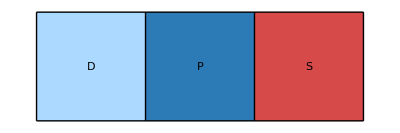

```mathematica
ArrayPlot[{mat[[3]]},ColorRules->{"P"->base⟦1⟧,"S"->base⟦2⟧,"D"->base⟦3⟧,"R"->base⟦4⟧},Epilog->{Black,MapIndexed[Style[Text[#1,Reverse[#2-1/2]],Black,50]&,Reverse[{mat[[3]]}],{2}]},Mesh->True,MeshStyle->Black]
```

Figure 1(c):

```mathematica
n={2,3,4,2,3,4,5,2, 3};
m={1,1,1,2,2,2,2,3, 3};
```

```mathematica
sets=Partition[Riffle[n,m],2]
```

{{2,1},{3,1},{4,1},{2,2},{3,2},{4,2},{5,2},{2,3},{3,3}}

```mathematica
maxvals=Table[4^Times[sets⟦i,1⟧,sets⟦i,2⟧],{i,1,Length[sets]}]
```

{16,64,256,256,4096,65536,1048576,4096,262144}

```mathematica
observedvals={10,20,35,76,430,1996,7882, 430, 8240}
```

{10,20,35,76,430,1996,7882,430,8240}

```mathematica
normalised=observedvals/maxvals
```

{5/8,5/16,35/256,19/64,215/2048,499/16384,3941/524288,215/2048,515/16384}

```mathematica
baselines=Table[Callout[{n⟦i⟧,m⟦i⟧,1},maxvals⟦i⟧],{i,1,Length[normalised],1}]
```

{Callout[{2,1,1},16],Callout[{3,1,1},64],Callout[{4,1,1},256],Callout[{2,2,1},256],Callout[{3,2,1},4096],Callout[{4,2,1},65536],Callout[{5,2,1},1048576],Callout[{2,3,1},4096],Callout[{3,3,1},262144]}

```mathematica
vals=Table[Callout[{n⟦i⟧,m⟦i⟧,normalised⟦i⟧},Appearance->"SlantedLabel"],{i,1,Length[normalised],1}]
```

{Callout[{2,1,5/8},Appearance→SlantedLabel],Callout[{3,1,5/16},Appearance→SlantedLabel],Callout[{4,1,35/256},Appearance→SlantedLabel],Callout[{2,2,19/64},Appearance→SlantedLabel],Callout[{3,2,215/2048},Appearance→SlantedLabel],Callout[{4,2,499/16384},Appearance→SlantedLabel],Callout[{5,2,3941/524288},Appearance→SlantedLabel],Callout[{2,3,215/2048},Appearance→SlantedLabel],Callout[{3,3,515/16384},Appearance→SlantedLabel]}

```mathematica
cols=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
BubbleChart[Join[baselines,vals],BubbleScale->"Diameter",ChartStyle->{cols⟦3⟧,cols⟦3⟧,cols⟦3⟧,cols⟦3⟧,cols⟦3⟧,cols⟦3⟧,cols⟦3⟧,cols⟦3⟧,cols⟦3⟧,cols⟦8⟧,cols⟦8⟧,cols⟦8⟧,cols⟦8⟧,cols⟦8⟧, cols[[8]], cols[[8]], cols[[8]], cols[[8]]},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of Strains (N)",18,Black],Style["Number of Antibiotics (M)",18,Black]}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"algooutput.pdf",%]
```

/Users/athreya/Desktop/projects/antibiotics-and-biodiversity/FigureSources/algooutput.pdf